```mathematica
Table[SphericalPlot3D[Abs[SphericalHarmonicY[3,m,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2*π},PlotRange->All,ImageSize->Small],{m,-2,2}] (* Angular Distribution *)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
a = 1;(* a is the Bohr Radius *)
R[n_,l_,r_]:=√((2/(n*a))^3 Factorial[n-l-1]/(2 n (Factorial[n+l])^3)) Exp[-r/(n*a)]*((2*r)/(n*a))^l*LaguerreL[n-l-1,2*l+1,(2*r)/(n*a)]/.n->3 (* Radial PDF *)
```

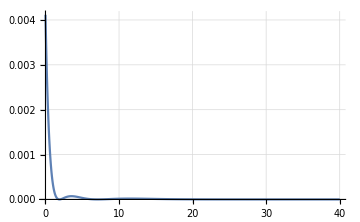
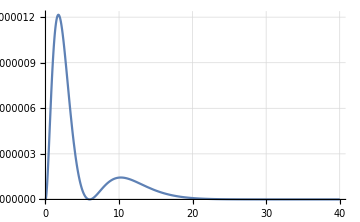
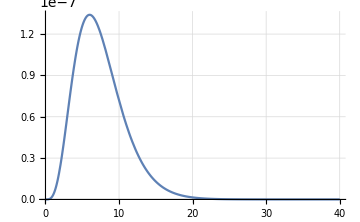

```mathematica
Table[Plot[Abs[R[3,l,r]]^2,{r,0,40},PlotRange->All,ImageSize->Medium,GridLines->Automatic],{l,0,2}]
```

```mathematica
F[n_,l_,m_,r_,θ_,ϕ_]:=R[n,l,r]*SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
Table[SphericalPlot3D[Abs[F[3,l,0,1/9,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2*π},ImageSize->Medium],{l,1,2}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Table[Integrate[x*(R[3,l,x])^2,{x,0,Infinity}],{l,0,2}]
```

{1/324,1/5184,1/129600}

```mathematica
Integrate[((1-2/3*x+2/27*x^2)*Exp[(- x)/3])^2*x,{x,0,Infinity}]
```

3/4

```mathematica
Integrate[((1-1/6*x)*x*Exp[(- x)/3])^2*x,{x,0,Infinity}]
```

243/32

```mathematica
243/32*64/(27^2*6)
```

1/9

```mathematica
Integrate[(x^2*Exp[(- x)/3])^2*x,{x,0,Infinity}]
```

10935/8

```mathematica
10935/8*16/(81^2*30)
```

1/9

```mathematica
R[3,0,x]
```

(ⅇ^(-x/3) (27-18 x+2 x^2))/(243 √3)

```mathematica
Integrate[(2/(√27) (1-2/3*x+2/27*x^2)*Exp[(- x)/3])^2,{x,0,Infinity}]
```

2/27

```mathematica
Conjugate[R[3,0,x]]
```

(ⅇ^(-Conjugate[x]/3) (27-18 Conjugate[x]+2 Conjugate[x]^2))/(243 √3)

```mathematica
FullSimplify[(ⅇ^(-Conjugate[x]/3) (27-18 Conjugate[x]+2 Conjugate[x]^2))/(243 √3),Assumptions->x ∈ Reals]
```

(ⅇ^(-x/3) (27+2 (-9+x) x))/(243 √3)

```mathematica
Cancel[(ⅇ^(-x/3) (27+2 (-9+x) x))/(243 √3)]
```

(ⅇ^(-x/3) (27-18 x+2 x^2))/(243 √3)

```mathematica
(ⅇ^(-x/3) (27-18 x+2 x^2))/(243 √3) == R[3,0,x]
```

True

```mathematica
R[1,0,x]
```

2 ⅇ^-x

```mathematica
Integrate[Abs[SphericalHarmonicY[1,0,θ,ϕ]]^2*(SphericalHarmonicY[1,1,θ,ϕ]-SphericalHarmonicY[1,-1,θ,ϕ]),{θ,0,Pi},{ϕ,0,2 Pi}]
```

0

```mathematica
Abs[SphericalHarmonicY[0,0,θ,ϕ]]^2
```

1/(4 π)

```mathematica
Abs[SphericalHarmonicY[1,0,θ,ϕ]]^2
```

(3 Abs[Cos[θ]]^2)/(4 π)

```mathematica
Abs[SphericalHarmonicY[1,1,θ,ϕ]]^2
```

(3 ⅇ^(-2 Im[ϕ]) Abs[Sin[θ]]^2)/(8 π)

```mathematica
Abs[SphericalHarmonicY[2,0,θ,ϕ]]^2
```

(5 Abs[-1+3 Cos[θ]^2]^2)/(16 π)

```mathematica
Integrate[Conjugate[(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])]*(r*Cos[θ])*(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])*(r^2*Sin[θ]),{r,0,Infinity},{θ,0,π},{ϕ,0,2 π}]
```

(128 √2)/729

```mathematica
Integrate[Conjugate[(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])]*(r*Sin[θ]*Cos[ϕ])*(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])*(r^2*Sin[θ]),{r,0,Infinity},{θ,0,π},{ϕ,0,2 π}]
```

0

```mathematica
Integrate[Conjugate[(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])]*(r*Sin[θ]*Sin[ϕ])*(F[1,0,0,r,θ,ϕ]+F[2,1,0,r,θ,ϕ])*(r^2*Sin[θ]),{r,0,Infinity},{θ,0,π},{ϕ,0,2 π}]
```

0